```mathematica
a=({{1, 0, 0, 0}, {0, 0, 0, 1}, {1, -((Pi^2)/18), 1, 0}, {0, 1, -((Pi^2)/18), 1}})
```

{{1,0,0,0},{0,0,0,1},{1,-π^2/18,1,0},{0,1,-π^2/18,1}}

```mathematica
b=({{0}, {0}, {((Pi^2)/144)*Cos[Pi/12]}, {((Pi^2)/144)*Cos[Pi/6]}})
```

{{0},{0},{((1+√3) π^2)/(288 √2)},{π^2/(96 √3)}}

```mathematica
LinearSolve[a,b]
```

{{0},{(-36 √3 π^2-√2 π^4-√6 π^4)/(32 (-324+π^4))},{(-9 √2 π^2-9 √6 π^2-√3 π^4)/(16 (-324+π^4))},{0}}

```mathematica
{(-36 √3 π^2-√2 π^4-√6 π^4)/(32 (-324+π^4))}//N
```

{0.136778}

```mathematica
{(-9 √2 π^2-9 √6 π^2-√3 π^4)/(16 (-324+π^4))}//N
```

{0.141201}

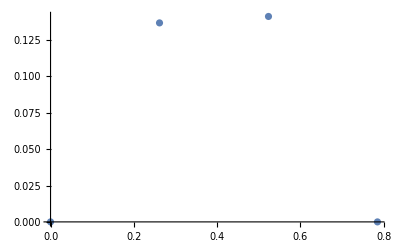

```mathematica
ListPlot[{{0,0},{Pi/12,((-36 √3 π^2-√2 π^4-√6 π^4)/(32 (-324+π^4)))},{Pi/6,((-9 √2 π^2-9 √6 π^2-√3 π^4)/(16 (-324+π^4)))},{Pi/4,0}}]
```